```mathematica
<<EccentricPN`
```

Computing kappaE

4.56205

Computing kappaJ

4.37664

## Definitions

```mathematica
etaOfq[q_]:=q/(1+q)^2
```

## Binary Parameters

```mathematica
idParams={e->0.4,q->1,n->0.012,eta->etaOfq[q],u->Pi}
```

{e→0.4,q→1,n→0.012,eta→q/(1+q)^2,u→π}

## Compute linear momentum for initial data

```mathematica
Py=eta Sqrt[Normal[jInne/EpsInne]]/Normal[rInne];
```

```mathematica
x0=Normal[rInne]/2;
```

```mathematica
twoPuncturesParams[x0_,Py_]:=
StringJoin[Riffle[
{"TwoPunctures::par_b = "<>ToString[x0,CForm],
"TwoPunctures::par_p_plus[1] = "<>ToString[Py,CForm],
"TwoPunctures::par_p_minus[1] = "<>ToString[-Py,CForm]},"\n"]]
```

```mathematica
x0//.idParams
```

11.8451

```mathematica
Py//.idParams
```

0.0430252

```mathematica
twoPuncturesParams[x0//.idParams,Py//.idParams]
```

TwoPunctures::par_b = 11.845073499262103
TwoPunctures::par_p_plus[1] = 0.04302515731159365
TwoPunctures::par_p_minus[1] = -0.04302515731159365

## Inspiral

```mathematica
genSoln[id_,tMax_]:=
EccentricSoln[xeModel,eta//.id,{Normal[xInne]//.id,e//.id,Pi//N,0},0,{0,tMax,1}]
```

```mathematica
tMax=1920;
```

```mathematica
soln=genSoln[idParams,tMax]
```

{r→InterpolatingFunction[{{0.,1920.}},<>],om→InterpolatingFunction[{{0.,1920.}},<>],phi→InterpolatingFunction[{{0.,1920.}},<>],x→InterpolatingFunction[{{-3.,1923.}},<>],e→InterpolatingFunction[{{-3.,1923.}},<>],u→InterpolatingFunction[{{0.,1920.}},<>],l→InterpolatingFunction[{{0.,1920.}},<>],h→InterpolatingFunction[{{0.,1920.}},<>],psi4→InterpolatingFunction[{{0.,1920.}},<>],psi4Om→InterpolatingFunction[{{0.,1920.}},<>],psi4Phi→InterpolatingFunction[{{0.,1920.}},<>]}

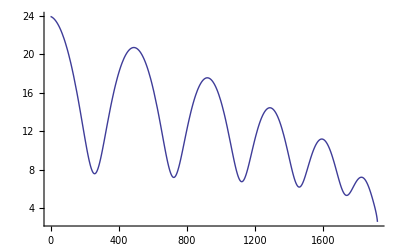

```mathematica
Plot[Evaluate[r[t]/.soln],{t,0,tMax},PlotRange->{0,All}]
```

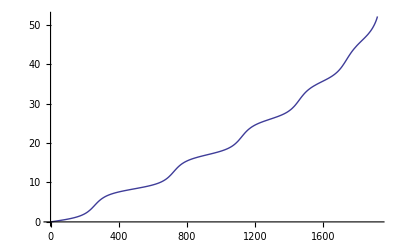

```mathematica
Plot[Evaluate[phi[t]/.soln],{t,0,tMax},PlotRange->{0,All}]
```

```mathematica
FindRoot[Evaluate[phi[t]/.soln]==4.Pi,{t,500}]
```

{t→720.196}

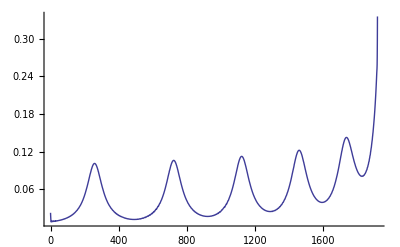

```mathematica
Plot[Evaluate[-psi4Om[t]/.soln],{t,0,tMax},PlotRange->{0,All}]
```

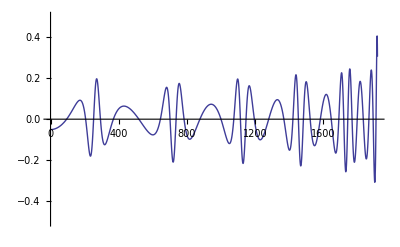

```mathematica
Plot[Evaluate[Re@h[t]/.soln],{t,0,tMax},PlotRange->{-0.5,0.5}]
```

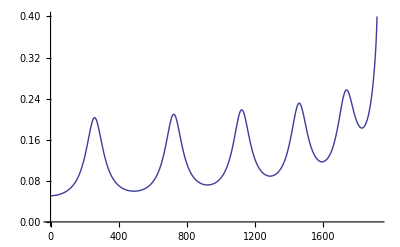

```mathematica
Plot[Evaluate[Abs@h[t]/.soln],{t,0,tMax},PlotRange->{0,0.4}]
```